```mathematica
Manipulate[Plot[Re[(r E^(I w))^x],{x,0,10},PlotRange->Full],{{r,1},0,1},{{w,Pi},0,Pi}]
```

```mathematica
nn=32;
Manipulate[PolarPlot[Abs[(r E^(I (2Pi)/nn))^n],{n,0,nn},PlotRange->All],{{r,1},0,1}]
```

```mathematica
Manipulate[Plot[SawtoothWave[x+d]-SawtoothWave[x-d],{x,0,3},PlotRange->{{0,3},{-1,1}}],{{d,.25},0,.5}]
```

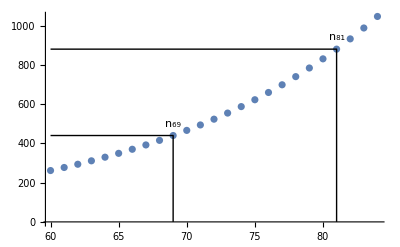

```mathematica
tuneF:=440;
Show[ListPlot[Table[{n,2^((n-69)/12) tuneF//N},{n,60+0,60+24,1}],
Epilog->{
Text["n_69",{69,500}],
Line[{{60,440},{69,440},{69,0}}],
Text["n_81",{81,940}],Line[{{60,880},{81,880},{81,0}}]}]]
```

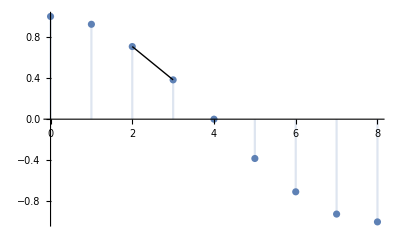

```mathematica
DiscretePlot[Sin[Pi/2+n (2Pi)/16],{n,0,8},Epilog->{Line[{{2,Sin[3 Pi/4]},{3,Sin[7 Pi/8]}}]}]
```